# E-cadherin islands

```mathematica
brachOutG={};
brachInG={};
octoutG = {};
octInG= {};
medianCellArea=35;
```

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@island analysis\\";
```

## Islands 1 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island1 Z23.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island1 Z23.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"\\oct4 island1 Z23.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

31

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,Thinning@boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0548248

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.138646

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.22883

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0721097

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
(*fig*)
```

```mathematica
{mask,brachcropped,octcropped}=(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.80]},{XYZColor[0,0,1,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.80]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

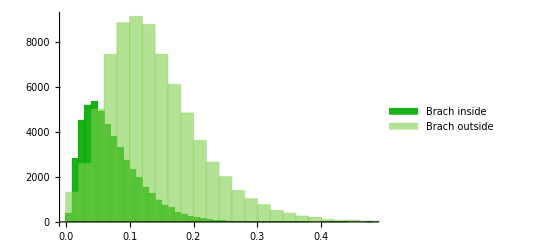

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,PlotRange->All,ChartLegends->{#3}]&,{{brachinside,brachoutside},
{Directive[Opacity[0.9],RGBColor[0, Rational[2, 3], 0]],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

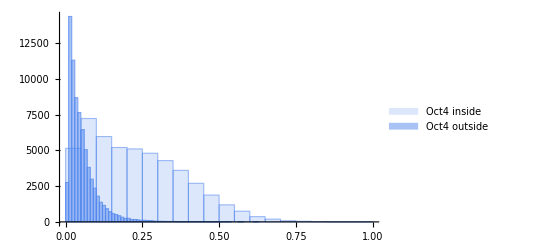

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},
{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.22883
Mean Intensity of Oct4 outside: 0.0548248

Mean Brach inside: 0.0721097
Mean Intensity of Brach outside: 0.138646

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.302075

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## Islands 2 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island2 Z37.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island2 Z37.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island2 Z37.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

32

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,Thinning@boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0469694

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0900223

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.113922

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0534231

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=ImageAdjust/@(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Magenta],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.80]},{XYZColor[1,0,0,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.83]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[0,1,1,0.65]],Style[1,XYZColor[0,0,1,0.2]]}],
ImageSize->Medium,Background-> Black]
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.82]},{XYZColor[0,0,1,0.25],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.82]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

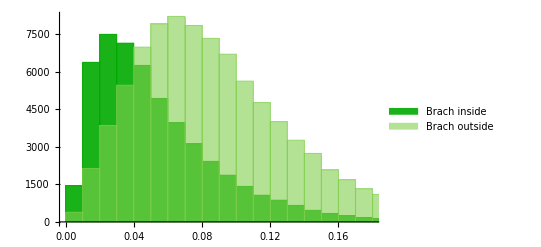

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

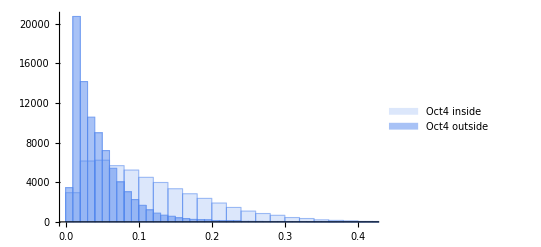

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.113922
Mean Intensity of Oct4 outside: 0.0469694

Mean Brach inside: 0.0534231
Mean Intensity of Brach outside: 0.0900223

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.299828

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## islands 3 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island3 Z18.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island3 Z18.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island3 Z18.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

30

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,Thinning@boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0512758

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.133302

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.166047

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0665688

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.80]},{XYZColor[0,0,1,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.80]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

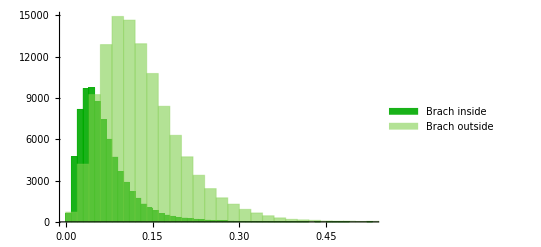

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3},PlotRange->All]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

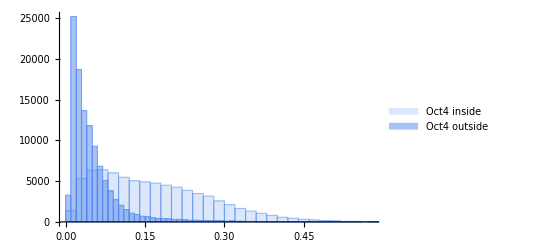

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.166047
Mean Intensity of Oct4 outside: 0.0512758

Mean Brach inside: 0.0665688
Mean Intensity of Brach outside: 0.133302

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.30768

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## islands 4 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island4 Z27.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island4 Z27.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island4 Z27.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

35

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,Thinning@boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway * oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0536478

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0993344

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.148729

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0455604

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.82]},{XYZColor[0,0,1,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.82]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

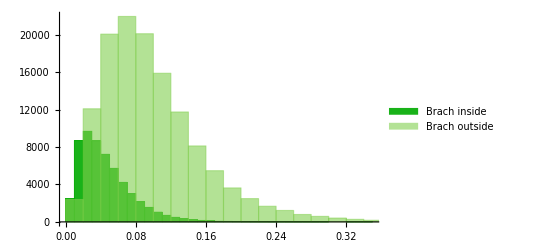

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3},PlotRange->All]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

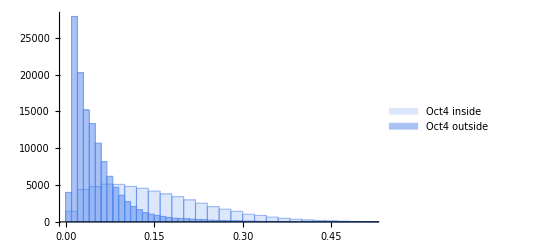

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.148729
Mean Intensity of Oct4 outside: 0.0536478

Mean Brach inside: 0.0455604
Mean Intensity of Brach outside: 0.0993344

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.293064

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## islands 5

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island5 Z48.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island5 Z48.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island5 Z48.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

45

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,Thinning@boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0331851

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0531644

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.0901638

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0313597

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.82]},{XYZColor[0,0,1,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.82]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

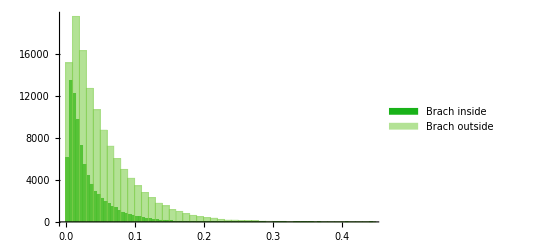

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3},PlotRange->All]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

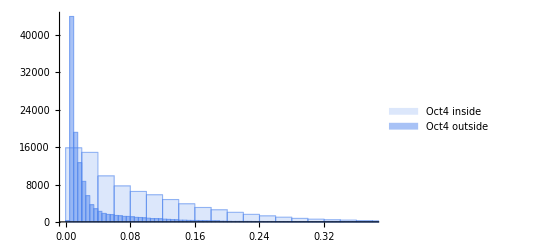

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.0901638
Mean Intensity of Oct4 outside: 0.0331851

Mean Brach inside: 0.0313597
Mean Intensity of Brach outside: 0.0531644

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.121836

## islands 6 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island6 Z13.tif"],1];
```

```mathematica
boundary=Pruning@boundary;
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island6 Z13.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island6 Z13.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

38

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[DeleteSmallComponents[filling,100],medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,DeleteSmallComponents[boundary,5]]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.0309726

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.108011

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.0911287

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0519854

```mathematica
ColorCombine[{Dilation[DeleteSmallComponents[boundary,5],1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=ImageAdjust/@(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.4],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.82]},{XYZColor[0,0,1,0.4],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.82]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

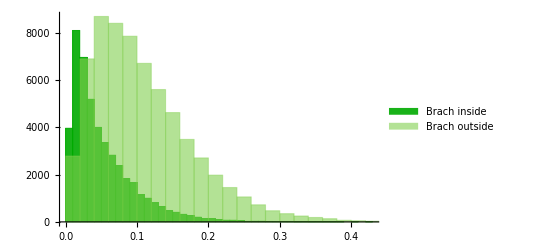

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3},PlotRange->All]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

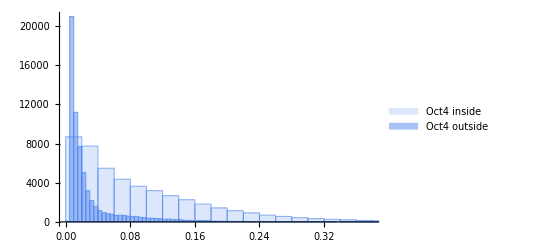

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.0911287
Mean Intensity of Oct4 outside: 0.0309726

Mean Brach inside: 0.0519854
Mean Intensity of Brach outside: 0.108011

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.215083

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## islands 7 ✓

```mathematica
boundary=Closing[Binarize@Import[dir<>"Mask island7 Z11.tif"],1];
```

```mathematica
brach=GaussianFilter[Import[dir<>"Brach island7 Z11.tif"],1];
```

```mathematica
oct=GaussianFilter[Import[dir<>"oct4 island7 Z11.tif"],1];
```

```mathematica
cells=DeleteBorderComponents@MorphologicalComponents[ColorNegate@boundary,CornerNeighbors->False];
```

```mathematica
cellimg=Image@Total[Values@ComponentMeasurements[cells,"Mask"]];
```

```mathematica
Image[ImageCrop[cellimg],ImageSize->Small]
```

-Graphics-

```mathematica
avgAreaperfectCell=Floor@Mean@Values@ComponentMeasurements[cells,"EquivalentDiskRadius"]
```

50

```mathematica
filling=FillingTransform@boundary;
```

```mathematica
imgBoundAway=Dilation[filling,medianCellArea]*ColorNegate[filling]Erosion[ColorNegate[boundary],1];
```

```mathematica
HighlightImage[imgBoundAway,boundary]//Image[#,ImageSize->Large]&
```

```mathematica
octoutside=imgBoundAway*oct;
brachoutside=imgBoundAway*brach;
```

```mathematica
octoutI=ImageMeasurements[octoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.049267

```mathematica
brachoutI=ImageMeasurements[brachoutside,"MeanIntensity",Masking->imgBoundAway]
```

0.189921

```mathematica
octinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*oct;
brachinside=Image[Total[Values@ComponentMeasurements[cells,"Mask"]]]*brach;
```

```mathematica
octinI=ImageMeasurements[octinside,"MeanIntensity",Masking->cellimg]
```

0.126672

```mathematica
brachinI=ImageMeasurements[brachinside,"MeanIntensity",Masking->cellimg]
```

0.0809082

```mathematica
ColorCombine[{Dilation[boundary,1],ImageAdd[brachinside,brachoutside],ImageAdd[octoutside,octinside]}, "RGB"];
```

```mathematica
{mask,brachcropped,octcropped}=ImageAdjust/@(ColorSeparate[-Graphics-])
```

```mathematica
Show[
Graphics[{{Directive[Opacity[0.2],Darker@Green],PointSize[0.008],Point@PixelValuePositions[brachcropped,1,0.65]},{XYZColor[0,0,1,0.2],PointSize[0.008],Point@PixelValuePositions[octcropped,1,0.65]}}],
HighlightMesh[ImageMesh[mask],{Style[2,XYZColor[1,0,0,0.65]],Style[1,XYZColor[1,0,0,0.2]]}],
ImageSize->Medium,Background-> Black]
```

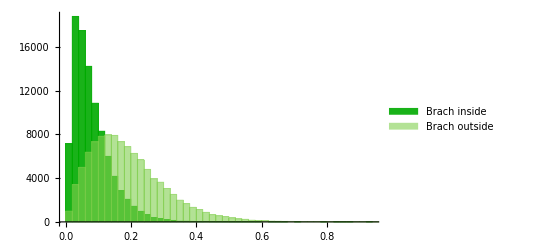

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3},PlotRange->All]&,{{brachinside,brachoutside},{Directive[Opacity[0.9],Darker@Green],Directive[Opacity[0.6],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]]},
{"Brach inside","Brach outside"}}]]
```

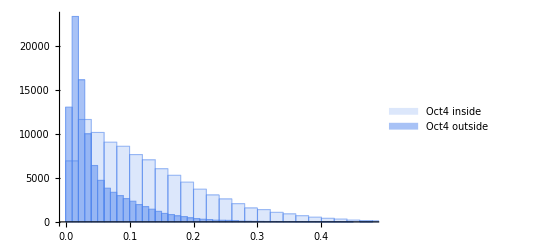

```mathematica
Show[MapThread[Histogram[DeleteCases[Flatten@ImageData[#1],0.],
ChartStyle->#2,ChartLegends->{#3}]&,{{octinside,octoutside},{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
{"Oct4 inside","Oct4 outside"}}]]
```

```mathematica
TableForm[{
{Style["Mean Intensity of Oct4 inside: "<> ToString[octinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Oct4 outside: "<> ToString[octoutI],Bold,18,RandomColor[]]},
{},
{Style["Mean Brach inside: "<> ToString[brachinI],Bold,18,RandomColor[]]},
{Style["Mean Intensity of Brach outside: "<> ToString[brachoutI],Bold,18,RandomColor[]]}
}]
```

Mean Intensity of Oct4 inside: 0.126672
Mean Intensity of Oct4 outside: 0.049267

Mean Brach inside: 0.0809082
Mean Intensity of Brach outside: 0.189921

```mathematica
{v1,v2}=Flatten@*ImageData/@{brach,oct};
```

```mathematica
Correlation[v1,v2]
```

0.349384

```mathematica
threadedData=Thread[{Flatten[ImageData@brachcropped],Flatten[ImageData@octcropped]}];
```

```mathematica
plt=ListPlot[threadedData,
PlotStyle->XYZColor[1,0,0,0.25],AxesStyle->Directive[Black,18],PlotRange->{{0,1},{0,1}},AxesLabel->{"I_Brachyury","I_Oct4"}]
```

-Graphics-

```mathematica
region=Region@ImplicitRegion[y+x-0.4≤0,{x,y}]
```

-Graphics-

```mathematica
filteredData=Select[threadedData,!#∈region&];
```

```mathematica
lm=Normal@LinearModelFit[filteredData,x,x]
```

0.474917-0.877246 x

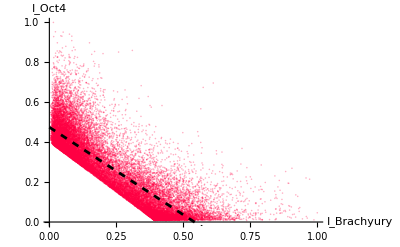

```mathematica
Show[ListPlot[filteredData,
PlotStyle->XYZColor[1,0,0,(0.5/GoldenRatio)],AxesStyle->Directive[Black,18],PlotRange->All,AxesLabel->{"I_Brachyury","I_Oct4"}],
Plot[lm,{x,0,0.58},PlotStyle->{Black,Thickness[0.005],Dashed}]
]
```

```mathematica
AppendTo[brachInG,DeleteCases[Flatten@ImageData[brachinside],0.]];
AppendTo[brachOutG,DeleteCases[Flatten@ImageData[brachoutside],0.]];
AppendTo[octInG,DeleteCases[Flatten@ImageData[octinside],0.]];
AppendTo[octoutG,DeleteCases[Flatten@ImageData[octoutside],0.]];
```

## Pooled results

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\analysis notebooks\\miscellaneous\\ecadherin islands\\EcadIslandSave.mx"];
```

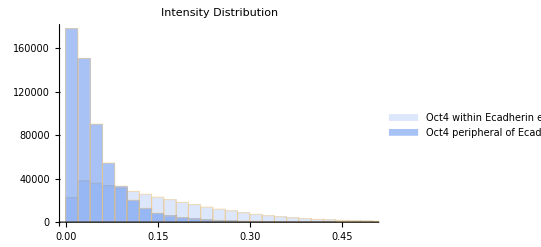

```mathematica
Histogram[{Flatten[octInG],Flatten[octoutG]},ChartStyle->{Directive[Opacity[0.2],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]],Directive[Opacity[0.5],RGBColor[0.32275413862236824, 0.5275986119945049, 0.9346586953071072]]},
AxesStyle->Thick,TicksStyle->Directive[Black, Thick, Italic],ChartLegends->Placed[{"Oct4 within Ecadherin expressing cells","Oct4 peripheral of Ecadherin expressing cells"},Right],
PlotLabel->Style["Intensity Distribution",Black,Italic,15],PlotRange->{{0,0.5},Automatic}]
```

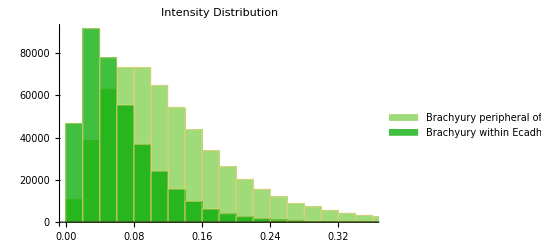

```mathematica
Histogram[{Flatten[brachOutG],Flatten[brachInG]},ChartStyle->{Directive[Opacity[0.75],RGBColor[0.5055041188968508, 0.8108045614478527, 0.30599762638806727]],Directive[Opacity[0.75],Darker@Green]},
AxesStyle->Thick,TicksStyle->Directive[Black, Thick, Italic],ChartLegends->Placed[{"Brachyury peripheral of Ecadherin expressing cells","Brachyury within Ecadherin expressing cells"},Right],
PlotLabel->Style["Intensity Distribution",Black,Italic,15]]
```

```mathematica
globalCorrelations={0.3021,0.2998,0.3077,0.2931,0.2151,0.3494};
```

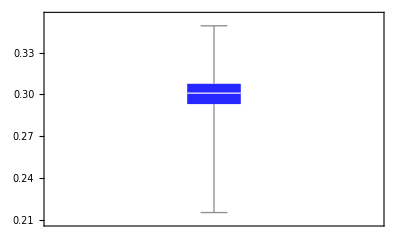

```mathematica
BoxWhiskerChart[globalCorrelations,ChartStyle->Directive[Opacity[0.85],Blue]]
```

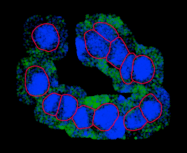
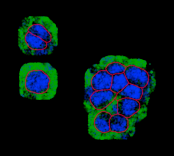
```mathematica
ImageCollage[{-Graphics-,-Graphics-,-Graphics-,ImageAdjust@-Graphics-,-Graphics-,-Graphics-},Background->Black]//Rasterize[#,"Image",ImageSize->1000]&
```

```mathematica
(*collage*)
```